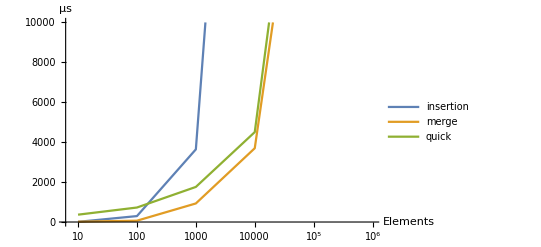

```mathematica
insertion = {{10,9}, {100,297}, {1000,3640}, {10000,42799}, {100000,2556887}, {1000000,255720556}};
merge = {{10,15}, {100, 66}, {1000, 930}, {10000, 3697},{100000, 24107}, {1000000, 138162}};
quick = {{10,368},{100,726},{1000,1758},{10000,4505},{100000,27079},{1000000,181452 }};

ListLogLinearPlot[{insertion, merge, quick}, PlotRange->{0,10000}, AxesLabel->{"Elements", "µs"}, Joined->True, PlotLegends-> {"insertion", "merge", "quick"}]
```

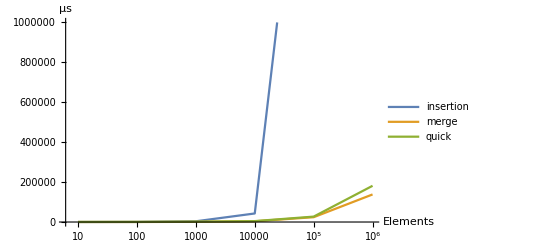

```mathematica
ListLogLinearPlot[{insertion, merge, quick}, PlotRange->{0, 1000000}, AxesLabel->{"Elements", "µs"}, Joined->True, PlotLegends-> {"insertion", "merge", "quick"}]
```